```mathematica
Clear["Global`*"] (*Clean All data*)
(*Needs["NumericalCalculus`"]*) (*ND is very SLOW*)
```

```mathematica
SetDirectory[NotebookDirectory[]](*Set directory for saving Output files with Wolfram notebook*)
Off[NIntegrate::izero]; (*Switch off warnings*)
Off[NIntegrate::nlim]; 
Off[General::stop];
Off[FunctionInterpolation::ncvb];
Off[NIntegrate::izero];
Off[NIntegrate::ncvb];
Off[NIntegrate::slwcon];
Off[StringJoin::string];
```

C:\Users\user\Dropbox\М5У\Research

100

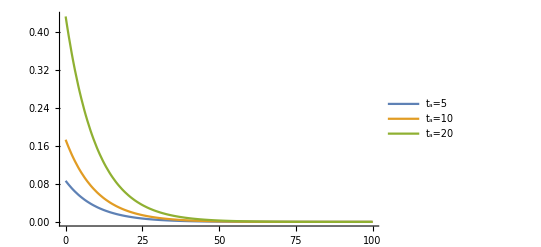

```mathematica
ClearAll[PdottINterp, table1,table2]
(*Setting material data*)
σzv=1.;c=σzv;
λ=0.1;(*α=0.0;*)β=1.0;γ=0.5;
(*Setting parameters of the tube*)
r1=1.0;r2=2.0;q=(r1/r2)^2; rmiddle=0.5*(r1+r2);
p0=1.; (*Reference pressure*)
ω0=1.;(*Frequency of oscillations*)
TimeIncr=10; (*Time during which pressure increases*)
tmax=100;(*Integration time*)
(*Setting an array for tabulating functions*)
ttab=Range[0.,tmax,0.001*tmax];
rtab=Range[r1,r2,0.001*(r2-r1)];
(*Helpful parameters for searching min and max values*)
myMin=-100;
myMax=100
(*Disturbance for y(0) in ODE, otherwise y(t)==0*)
ε=10.0^(-10);

(*Material Functions(MF) for R (t)and Π(t)*)
(*α1=0.0;*)
Π[t_]:=(*α1*t+*)β-γ*Exp[-λ*t](*λ>0, α,β≥ 0, γ∈[0,β]*)
(*Kelvin model*)
A=1/β;B=γ/(β(β-γ));μ=(β*λ)/(β-γ);
R[t_]:=A+B*Exp[-μ*t];
(*Π[t_]:=B+A*t^u*)(*u∈(0,1s)*)
Φ1[x_]:=c*Log[σzv/(σzv-x) ](*x∈[0,σzv)*)
φ1[u_]:= σzv*(1-Exp[-u/c])
Φ2[x_]:=x(*x∈[0,σzv)*)
φ2[u_]:= u
α=0.5; AA=1;
Φ3[x_]:=(x/AA)^(1./α)*Sign[x];(*x∈[0,σzv)*)
φ3[u_]:= AA*u^α;
(*Putting all MF into one list*)
φx={φ1,φ2,φ3};
Numφ=Length[φx];


p1[t_,ω_,p0_]:=p0(*p0;*)(*If[t<20,p0*t/20,p0]*)(**(1+1/10*Sin[ω*t])*)(* Pressure inside tube at radius Subscript[r, 1]*)
p2[t_,ω_,p0_]:=0 (*Pressure outside tube at radius Subscript[r, 2]*)
dp[t_,ω_,p0_]:=p1[t,ω,p0]-p2[t,ω,p0](*Pressure drop *)
dpdt[t_,ω_,p0_]:=D[dp[t1,ω,p0],t1]/.t1->t
z[t_,ω_,p0_]:=Sign[dp[t,ω,p0]]
(*LΠ[func_Symbol,t_?NumericQ,ω_?NumericQ,p0_?NumericQ]:=NIntegrate[Π[t-ξ]*D[func[ξ1,ω,p0],ξ1]/.ξ1-> ξ, {ξ, 0, t},Method->{Automatic,"SymbolicProcessing"->False}]+func[0,ω,p0]Π[t];
LR[func_Symbol,r_,t_]:=NIntegrate[R[t-ζ]*D[func[r,ζ1],ζ1]/.ζ1->ζ, {ζ, 0, t},Method->{Automatic,"SymbolicProcessing"->False}]+func[r,0]R[t];
*)

(*Normal Mode if load programm in smooth, i.e. for C^1 continuous functions*)
Pdott[dp_Symbol,dpdt_Symbol,t_?NumericQ, ω_, p_]:=Sqrt[3.](Π[0]*(dpdt[t,ω,p])+NIntegrate[Π'[t1]*dpdt[t1,ω,p],{t1,0,t},Method->{Automatic,"SymbolicProcessing"->False}]+dp[t,ω,p]*Π'[t])
(*Special Mode if load programm in not smooth but continuos, i.e. for the C^0 continuous function*)
(*Pdott[dp_Symbol,dpdt_Symbol,t_?NumericQ, TimeIncr_, p_]:=(Sqrt[3]*p/TimeIncr)*(NIntegrate[Π'[t-τ],{τ,0,Min[t,TimeIncr]},Method->{Automatic,"SymbolicProcessing"->False}] + Π[0]*HeavisideTheta[TimeIncr-t])*)
Plot[{Pdott[dp,dpdt,t, ω, 1], Pdott[dp,dpdt,t, ω, 2],Pdott[dp,dpdt,t, ω, 5]},{t,0,tmax}, PlotRange->All, PlotLegends->{"t_a=5","t_a=10","t_a=20"}]
xdt1={0.02*tmax,0.05*tmax};
xdt2={0.9*tmax,-0.05*tmax};
xdr1={r1+0.02*(r2-r1),0.05*(r2-r1)};
xdr2={r1+0.9*(r2-r1),-0.05*(r2-r1)};
xarr=Association[{Kpdot->{xdt1,xdt1,xdt1,xdr1}  ,Kmyy-> {xdt2,xdt2,xdt2,xdr2},Kur->{xdt2,xdt2,xdt2,xdr1},Kepsr->{xdt2,xdt2,xdt2,xdr1},Kepsint->{xdt2,xdt2,xdt2,xdr1},Kσint->{xdt2,xdt2,xdt2,xdr1},Kσr->{xdt1,xdt1,xdt1,xdr1},Kσθ->{xdt1,xdt1,xdt1,xdr1},Kσz->{xdt1,xdt1,xdt1,xdr1}}];
(*List of unknown function names. It is like keys in dictionaries*)
MyKeys={Kmyy,Kur,Kepsr,Kepsint,Kσint,Kσr,Kσθ,Kσz};
(*Function names (label) in the graph*)
GraphLabel=Association[{Kpdot->  "√3Π'[dp]",Kmyy-> "y",Kur->"u_r",Kepsr->"ε_r",Kepsint->"ε_int",Kσint->"σ_int",Kσr->"σ_r",Kσθ->"σ_θ",Kσz->"σ_z"}];
(*For a given function calculates f(r1,t),f(rmiddle,t),f(r2,t),f(r,tmax) for numerical solution and theretical one*)
ncalcf[var_Symbol,tt_,rt_]:={Transpose[{tt,var[r1,#]&/@tt}],Transpose[{tt,var[rmiddle,#]&/@tt}],Transpose[{tt,var[r2,#]&/@tt}],Transpose[{rt,var[#,tmax]&/@rt}]};
theorf[var_Symbol, TimeIncr_,p_]:=Module[{},(*Print[var];*){Transpose[{ttab,var[r1,#,TimeIncr,p]&/@ttab}],Transpose[{ttab,var[rmiddle,#,TimeIncr,p]&/@ttab}],Transpose[{ttab,var[r2,#,TimeIncr,p]&/@ttab}],Transpose[{rtab,var[#,tmax,TimeIncr,p]&/@rtab}]}];
```

# Linear Case φ2(u)=u. Analytical Solution

```mathematica
yth[r_,t_, ω_, p_]:=Sqrt[3.]/(1.-q)dp[t,ω,p]*γ*(1.-Exp[-λ*t])*(r/r);
Pdotth[r_,t_,ω_,p_]:=Sqrt[3.]*dp[t,ω,p]*γ*λ*Exp[-λ*t]*(r/r);
urth[r_,t_, ω_, p_]:=Sqrt[3.]/2 yth[r,t,ω,p]/r r1^2;
εrth[r_,t_, ω_, p_]:=-r1^2/r^2 Sqrt[3.]/2. yth[r,t,ω,p];εθth[r_,t_,ω_,p_]:=-εrth[r,t,ω,p];
Rth[r_,t_, ω_, p_]:=Sqrt[3]/(1.-q)dp[t,ω,p]*γ*λ(A/λ*(1.-Exp[-λ*t])+(B*Exp[-μ*t])/(μ-λ)(Exp[(μ-λ)t]-1.))*(r/r)
σrth[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)(1.-(r1/r)^2)Rth[ r,t,ω,p];
σθth[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)(1.+(r1/r)^2)Rth[ r,t,ω,p];
σzth[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)Rth[ r,t,ω,p];
εintth[r_,t_, ω_, p_]:=yth[r,t,ω,p]*(r1/r)^2;
σintth[r_,t_, ω_, p_]:=Rth[ r,t,ω,p]*(r1/r)^2;
```

# Power function Case φ3(u)=AA*u^α. Analytical Solution.

```mathematica
P[t_,ω_,p_]:=Sqrt[3]*dp[t,ω,p]*γ*α*1/(AA*(1-q^α));
RRth2[t_,ω_,p_]:=P[t,ω,p]*λ((A-A ⅇ^(-t λ))/λ-(B (ⅇ^(-t λ)-ⅇ^(-t μ)))/(λ-μ));(*R[|y|^a]*)
y2th[r_,t_,ω_,p_]:=(P[t,ω,p]*(1-Exp[-λ*t]))^(1/α)*(r/r);
ur2th[r_,t_, ω_, p_]:=Sqrt[3.]/2*y2th[r,t,ω,p]/r*r1^2;
εr2th[r_,t_, ω_, p_]:=-r1^2/r^2 Sqrt[3.]/2. y2th[r,t,ω,p];εθth[r_,t_,ω_,p_]:=-εrth[r,t,ω,p];
σr2th[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3. α)AA(1.-(r1/r)^(2*α))RRth2[ t,ω,p];
σθ2th[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3. α)AA(1.+(2.*α-1.)(r1/r)^(2*α))RRth2[ t,ω,p];
σz2th[r_,t_, ω_, p_]:=-p1[t,ω,p]+z[t,ω,p]/(√3. α)*AA*(1.+(α-1.)*(r1/r)^(2*α))*RRth2[ t,ω,p];
εint2th[r_,t_, ω_, p_]:=y2th[r,t,ω,p]*(r1/r)^2;
σint2th[r_,t_, ω_, p_]:=RRth2[t,ω,p]*AA*(r1/r)^(2α);
```

# Exponent function Case φ1(u)=σzv*(1-Exp[-u/c]). Analytical Solution.

```mathematica
y3th[r_,t_,ω_,p_]:=Chop[y/.FindRoot[t==-Log[1+σzv/(Sqrt[3]*γ*p)(ExpIntegralEi[-y/σzv]-ExpIntegralEi[-q*y/σzv] + Log[q])]/λ,{y,ε}][[1]]]
ur3th[r_,t_, ω_, p_]:=Sqrt[3.]/2*y3th[r,t,ω,p]/r*r1^2;
εr3th[r_,t_, ω_, p_]:=-r1^2/r^2 Sqrt[3.]/2. y3th[r,t,ω,p];εθth[r_,t_,ω_,p_]:=-εrth[r,t,ω,p];
εint3th[r_,t_, ω_, p_]:=y3th[r,t,ω,p]*(r1/r)^2;
```

```mathematica
(*Module for numerical simulations, define frequency (if there is no frequency in load function, then it doesn't matter), pressure amplitude, Index of MF from φx*)
BigData[ω_,p_,Nφ_Integer]:=Block[{PdottINterp, ymax, tt, rt,tablepdot,tableMyY,tableur, tableepsr,tableepsint,tableσint,tableσr,tableσθ,tableσz,solv, myy, ur,εr,εint,εθ,εz,F,F0t,dFr,dFdtr,LRdF,LRφ,σint,σr,σθ,σz, φloc,ty},
φloc=φx[[Nφ]];
Print["Setting MF φ[",Nφ,"]=",φloc];
(*Firstly, we tabulate values for Pdot(t) and F(s) in order to get values cheaply*)
PdottINterp=Interpolation[Table[{t,Pdott[dp,dpdt,t,TimeIncr,p]},{t,0,tmax,0.001tmax}],InterpolationOrder->3, Method->"Spline"];
F0t=Interpolation[Table[{b,NIntegrate[φloc[x]/x,{x,0,b}]},{b,0,ymax,0.1}],InterpolationOrder->3, Method->"Spline"];
F[ a_?NumericQ, b_?NumericQ]:=F0t[b]-F0t[a];

(*Secondly, we calculate y(t) from ODE, y[0]=ϵ is a small disturbance*)
myy=First[y/.NDSolve[{y'[t]==(y[t]*PdottINterp[t])/(φloc[y[t]]-φloc[q*y[t]]), y[0]==ε},y,{t, 0,tmax}, Method->{"DoubleStep",Method->"StiffnessSwitching"}]];
ymax=1.5*myy[tmax];(*It is necessary for Tabulating*)
ur[r_,t_]:=1./r(√3.)/2.*r1^2*myy[t];
εr[r_,t_]:=-1./r^2(√3.)/2.*r1^2*myy[t];
εint[r_,t_]:=myy[t]*(r1/r)^2;

dFr[r_,t_]:=F[(r1/r)^2*Abs[myy[t]],Abs[myy[t]]];
dFdtr[r_,t_]:=(φloc[Abs[myy[t]]]-φloc[Abs[myy[t]]*(r1/r)^2])myy'[t]/myy[t];
LRdF=Interpolation[Flatten[Table[{{r,t},NIntegrate[R[t-ζ]*dFdtr[r,ζ], {ζ, 0, t},Method->{Automatic,"SymbolicProcessing"->False}]},{r,r1,r2,0.01*r2},{t,0.,tmax, 0.01tmax}],  1],InterpolationOrder->3, Method->"Spline"];
LRφ=Interpolation[Flatten[Table[{{r,t},(r1/r)^2*NIntegrate[R[t-ζ]*φloc'[Abs[myy[ζ]]*(r1/r)^2]*myy'[ζ]*Sign[myy[ζ]], {ζ, 0, t},Method->{Automatic,"SymbolicProcessing"->False}]},{r,r1,r2,0.1*r2},{t,0.,tmax, 0.01tmax}],  1],InterpolationOrder->3, Method->"Spline"];

σint[r_,t_]:=LRφ[r,t];
σr[r_,t_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)LRdF[ r,t];
σθ[r_,t_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)(LRdF[ r,t]+2.*LRφ[r,t]);
σz[r_,t_]:=-p1[t,ω,p]+z[t,ω,p]/(√3.)(LRdF[ r,t]+      LRφ[r,t]);
tt=Range[0.,tmax,0.01*tmax];
rt=Range[r1,r2,0.01*(r2-r1)];
tablepdot=Transpose[{tt,PdottINterp[tt]}];
ty=Transpose[{tt,myy[tt]}];
tableMyY={ty,ty,ty,ty};
Association[{Kpdot-> tablepdot,Kmyy-> tableMyY,Kur->ncalcf[ur,tt,rt],Kepsr->ncalcf[εr,tt,rt],Kepsint->ncalcf[εint,tt,rt],Kσint->ncalcf[σint,tt,rt],Kσr->ncalcf[σr,tt,rt],Kσθ->ncalcf[σθ,tt,rt],Kσz->ncalcf[σz,tt,rt],KLRdF-> ncalcf[LRdF,tt,rt], KLRφ-> ncalcf[LRφ,tt,rt]}]
];



BigDataTheory[ω_,p_]:=Block[{},
Association[{Kpdot->  theorf[Pdotth,ω,p],Kmyy->  theorf[yth,ω,p],Kur->theorf[urth,ω,p],Kepsr->theorf[εrth,ω,p],Kepsint->theorf[εintth,ω,p],Kσint->theorf[σintth,ω,p],Kσr->theorf[σrth,ω,p],Kσθ->theorf[σθth,ω,p],Kσz->theorf[σzth,ω,p],KLRdF-> theorf[Rth,TimeIncr,p], KLRφ-> theorf[Rth,TimeIncr,p]}]
]
BigDataTheory2[ω_,p_]:=Block[{},
Association[{Kpdot->  theorf[Pdotth,ω,p],Kmyy-> theorf[y2th,ω,p],Kur->theorf[ur2th,ω,p],Kepsr->theorf[εr2th,ω,p],Kepsint->theorf[εint2th,ω,p],Kσint->theorf[σint2th,ω,p],Kσr->theorf[σr2th,ω,p],Kσθ->theorf[σθ2th,ω,p],Kσz->theorf[σz2th,ω,p]}]
]
BigDataTheory3[ω_,p_]:=Block[{},
Association[{Kpdot->  theorf[Pdotth,ω,p],Kmyy-> theorf[y3th,ω,p],Kur->theorf[ur3th,ω,p],Kepsr->theorf[εr3th,ω,p],Kepsint->theorf[εint3th,ω,p]}]
]
MyRange[list_]:=Block[{minv, maxv,fv,lv},fv=First[list][[2]];lv= Last[list][[2]];
minv=Max[Min[fv,lv],myMin];maxv=Min[Max[fv,lv],myMax];(*Print[fv<>lv<>minv<>maxv];Print[list];*){minv,maxv}];
SetOptions[ListLinePlot,ImageSize->400,Ticks->{Range[0,tmax,10],Range[-10,10,.5]},AxesLabel->Automatic,LabelStyle->Directive[Black,Bold], PlotRange-> Full,PlotStyle->{{Blue,Thickness[0.01]},{Red,Dotted},{Green,Thickness[0.01]},{Orange ,Dotted},{Gray,Thickness[0.01]},{Yellow,Dotted},{Purple,Thickness[0.01]},{Cyan,Dotted},{Brown,Thickness[0.01]},
{Magenta,Dotted}}, Ticks->Automatic];
SetOptions[ListLogLogPlot,ImageSize->400,Ticks->{Range[0,tmax,10],Range[-10,10,.5]},AxesLabel->Automatic,LabelStyle->Directive[Black,Bold], PlotRange-> Full,PlotStyle->{{Blue,Thickness[0.01]},{Red,Dotted},{Green,Thickness[0.01]},{Orange ,Dotted},{Gray,Thickness[0.01]},{Yellow,Dotted},{Purple,Thickness[0.01]},{Cyan,Dotted},{Brown,Thickness[0.01]},
{Magenta,Dotted}}, Ticks->Automatic];
Xcoor[x_,dx_,Num_,i_]:=x+dx*Mod[i-1,Num];
Epi[x_, dx_, Num_,tab_, names_]:=Module[{xarr, posX,coorX, Ntab, ran},Ntab=Length[tab];posX=ConstantArray[{},Ntab];coorX=ConstantArray[{},Ntab];ran=Range[1,Ntab];
Do[
coorX[[i]]=Xcoor[x,dx,Num,i];xarr=#1&@@@tab[[i]];posX[[i]]=Position[xarr,Nearest[xarr,coorX[[i]]][[1]]][[1,1]],
{i,ran}
];
{Epilog->{Table[(Style[Text[names[[i]],{coorX[[i]],tab[[i]][[posX[[i]]]][[2]]}],12,Background->White]),{i,ran}]}}]

PrintPlots[list_,Num_,var_,xarr_,names_, listname_]:=Module[{},SetOptions[ListLinePlot,AxesLabel->{Style["t",Bold,Larger], Style[GraphLabel[var],Bold,Larger]},Frame->{True,True,False,False},FrameStyle->Directive[13,Italic],FrameLabel->{"t",GraphLabel[var]},PlotRangeClipping->False,PlotRange-> {{0,tmax},Automatic}];
Print[
ListLinePlot[list[[1]],PlotLabel->GraphLabel[var]<>" (t) r=r_1", Evaluate[Epi[xarr[[1,1]],xarr[[1,2]],Num,list[[1]], names]],PlotLegends->Evaluate[listname[[1]]]  ],
(*ListLinePlot[list[[2]],PlotLabel->GraphLabel[var]<>" (t) r=r_m", PlotRange-> Full, Evaluate[Epi[xarr[[2,1]],xarr[[2,2]],Num,list[[2]], names]]],*)
ListLinePlot[list[[3]],PlotLabel->GraphLabel[var]<>" (t) r=r_2", (*PlotRange-> Full,*) Evaluate[Epi[xarr[[3,1]],xarr[[3,2]],Num,list[[3]], names]]],
ListLinePlot[list[[4]],PlotLabel->GraphLabel[var]<>" (r) t=t_max", PlotRange-> Full, Evaluate[Epi[xarr[[4,1]],xarr[[4,2]],Num,list[[4]], names]],FrameLabel->{"r",GraphLabel[var]}]
]];

PrintLogLogPlots[list_,Num_,var_,xarr_,names_, listname_]:=Module[{},SetOptions[ListLogLogPlot,AxesLabel->{Style["t",Bold,Larger], Style[GraphLabel[var],Bold,Larger]},Frame->{True,True,False,False},FrameStyle->Directive[13,Italic],FrameLabel->{"t",GraphLabel[var]},PlotRangeClipping->False,PlotRange-> {{0,tmax},Automatic}];
Print[
ListLogLogPlot[Abs@list[[1]],PlotLabel->GraphLabel[var]<>" (t) r=r_1", Evaluate[Epi[xarr[[1,1]],xarr[[1,2]],Num,list[[1]], names]],PlotLegends->Evaluate[listname[[1]]]  ],
(*ListLogLogPlot[list[[2]],PlotLabel->GraphLabel[var]<>" (t) r=r_m", PlotRange-> Full, Evaluate[Epi[xarr[[2,1]],xarr[[2,2]],Num,list[[2]], names]]],*)
ListLogLogPlot[Abs@list[[3]],PlotLabel->GraphLabel[var]<>" (t) r=r_2", (*PlotRange-> Full,*) Evaluate[Epi[xarr[[3,1]],xarr[[3,2]],Num,list[[3]], names]]],
ListLogLogPlot[Abs@list[[4]],PlotLabel->GraphLabel[var]<>" (r) t=t_max", PlotRange-> Full, Evaluate[Epi[xarr[[4,1]],xarr[[4,2]],Num,list[[4]], names]],FrameLabel->{"r",GraphLabel[var]}]
]];

figcompare[var_,Parr_, names_, xarr_]:=Module[{list, listname,iφ, j,col, Num, k},
list=ConstantArray[{},4];listname=ConstantArray[{},4];
iφ=2;Num=2;k=0;
Do[
Do[
list[[col]]=Append[list[[col]],arr[[j,iφ]][var][[col]]];
list[[col]]=Append[list[[col]],arrtheor[[j]][var][[col]]];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>"p="<>ToString[ptable[[j ]] ]<>", ЧР"];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>"p="<>ToString[ptable[[j ]] ]<>", ТР"],
{j,Parr}],
{col,{1,2,3,4}}];
PrintPlots[list,Num,var,xarr,names, listname];]

figcompare2[var_,Parr_, names_, xarr_]:=Module[{list, listname, iφ, j,col,Num,k},
list=ConstantArray[{},4];listname=ConstantArray[{},4];
iφ=3;Num=2;k=0;
Do[
Do[
list[[col]]=Append[list[[col]],arr[[j,iφ]][var][[col]]];
list[[col]]=Append[list[[col]],arrtheor2[[j]][var][[col]]];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>", ЧР"];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>", ТР"],
{j,Parr}],
{col,{1,2,3,4}}];
PrintPlots[list,Num,var,xarr,names,listname];]

figcompare3[var_,Parr_, names_, xarr_]:=Module[{list, listname, iφ, j,col,Num,k},
list=ConstantArray[{},4];listname=ConstantArray[{},4];
iφ=1;Num=2;k=0;
Do[
Do[
list[[col]]=Append[list[[col]],arr[[j,iφ]][var][[col]]];
list[[col]]=Append[list[[col]],arrtheor3[[j]][var][[col]]];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>", ЧР"];
k++;listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>", ТР"],
{j,Parr}],
{col,{1,2,3,4}}];
PrintPlots[list,Num,var,xarr,names,listname];]


figgen[var_,Parr_,Nφarr_, names_, xarr_]:=Module[{list,listname, i, j,col, Num,k},
list=ConstantArray[{},4];listname=ConstantArray[{},4]; Num=Length[Nφarr];k=0;
Do[
Do[
Do[
(*Print["Nfi="<>ToString[i]<>" Parr="<>ToString[j]<>" col="<>ToString[col]];*)
k++;
list[[col]]=Append[list[[col]],arr[[j,i]][var][[col]]];
listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>" φ="Subscript["φ",i]],
{i,Nφarr}],
{j,Parr}],
{col,{1,2,3,4}}];
PrintPlots[list,Num,var,xarr,names,listname];]

figgenLog[var_,Parr_,Nφarr_, names_, xarr_]:=Module[{list,listname, i, j,col, Num,k},
list=ConstantArray[{},4];listname=ConstantArray[{},4]; Num=Length[Nφarr];k=0;
Do[
Do[
Do[
(*Print["Nfi="<>ToString[i]<>" Parr="<>ToString[j]<>" col="<>ToString[col]];*)
k++;
list[[col]]=Append[list[[col]],arr[[j,i]][var][[col]]];
listname[[col]]=Append[listname[[col]],ToString[k]<>": p="<>ToString[ptable[[j ]] ]<>" φ="Subscript["φ",i]],
{i,Nφarr}],
{j,Parr}],
{col,{1,2,3,4}}];
PrintLogLogPlots[list,Num,var,xarr,names,listname];]
```

```mathematica
AbsoluteTiming[
ptable=(*{1, 1.5,1.6,1.65, 1.7}*)(*{0.1,0.2,  0.3,0.4, 0.5}*)Range[0.1,2,0.5];
Nφtable={1,2,3}(*Range[1,3]*);
Np=Length[ptable];
Nφ=Length[Nφtable];
arr=ParallelTable[Quiet[BigData[ω,pp,Nφ]],{pp,ptable},{Nφ,Nφtable}];
]
AbsoluteTiming[
arrtheor=ParallelTable[Quiet[BigDataTheory[1,pp]],{pp,ptable}];
arrtheor2=ParallelTable[Quiet[BigDataTheory2[1,pp]],{pp,ptable}];
arrtheor3=ParallelTable[Quiet[BigDataTheory3[1,pp]],{pp,ptable}];
Print["Done"]
]
```

{684.244,Null}

Done

{358.041,Null}

## All Results

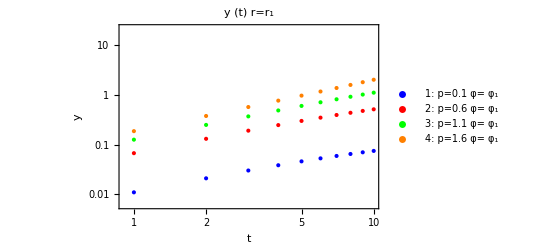
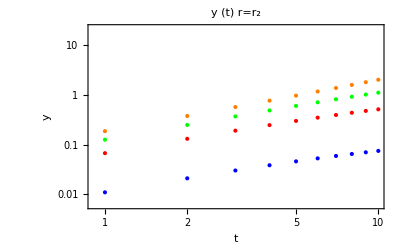
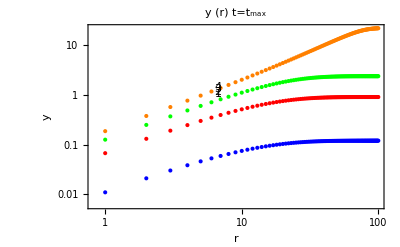

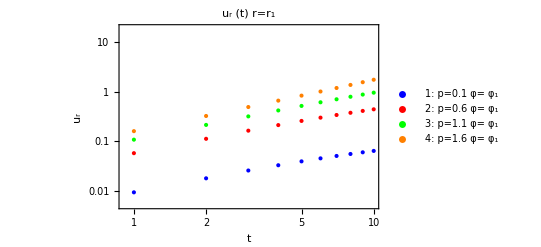
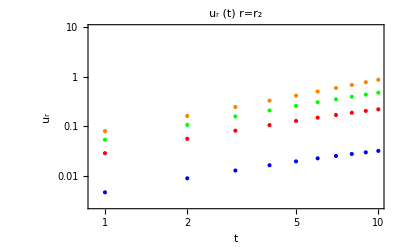
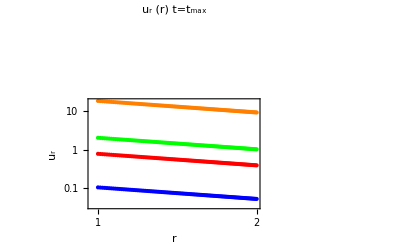

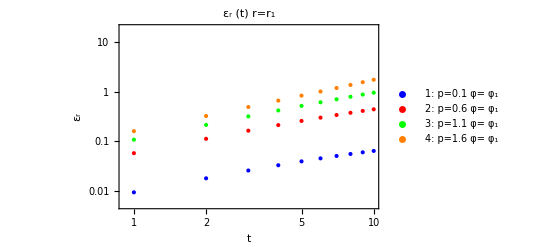
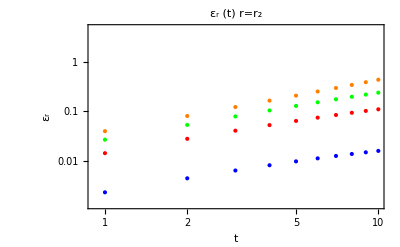

```mathematica
(*Do[Quiet[figgen[var,Range[1,Np],Range[1,Nφ],Range[1,Nφ*Np],xarr[var]]],{var, MyKeys}]*)
tmax=10;
Do[Quiet[figgenLog[var,Range[1,Np],{1},Range[1,1*Np],xarr[var]]],{var, MyKeys}]
```

## Results Exp fi Case

100

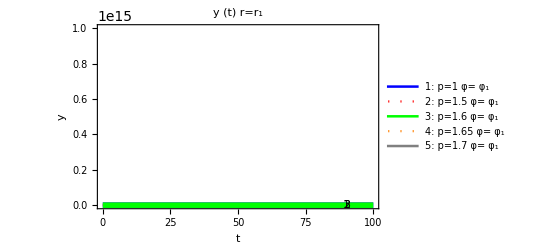
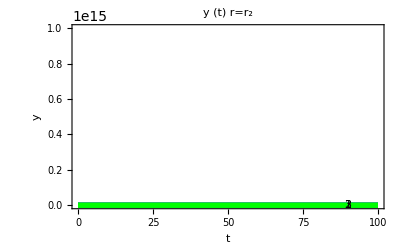
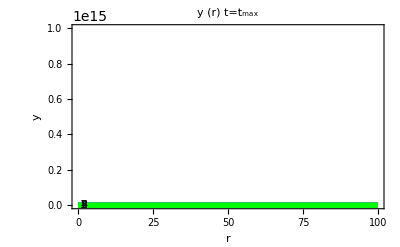

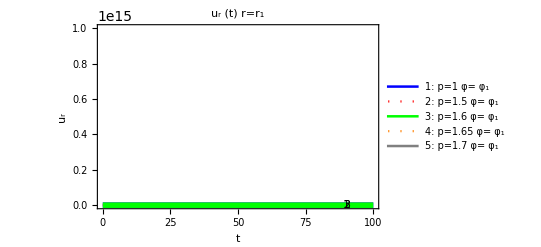
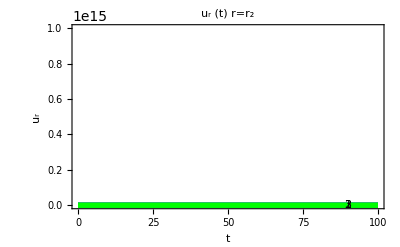
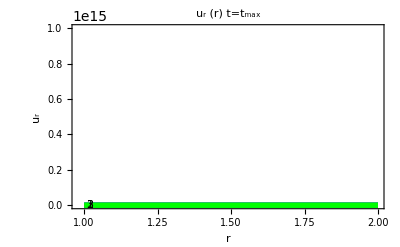

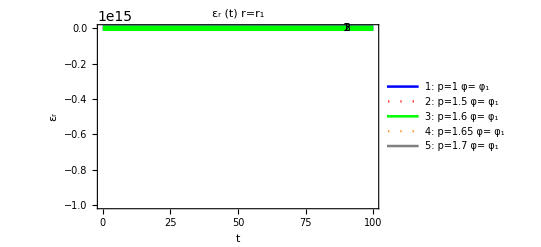
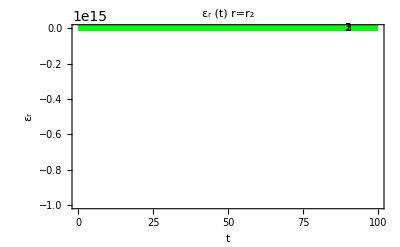

```mathematica
tmax=100
Do[Quiet[figgen[var,Range[1,Np],{1},Range[1,Np],xarr[var]]],{var, MyKeys}]
```

## Linear Case

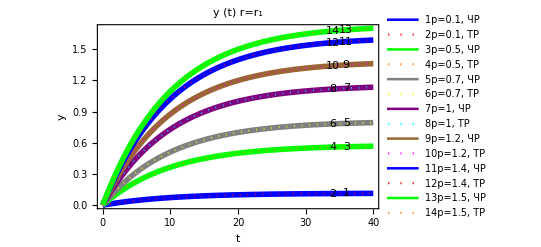
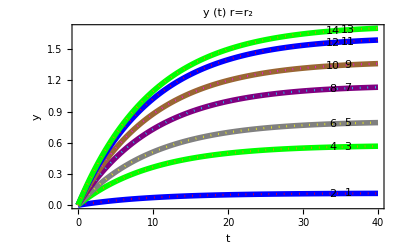
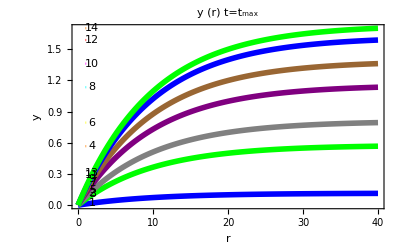

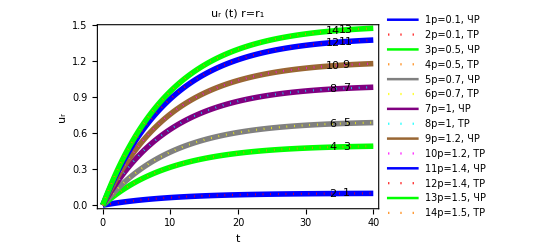
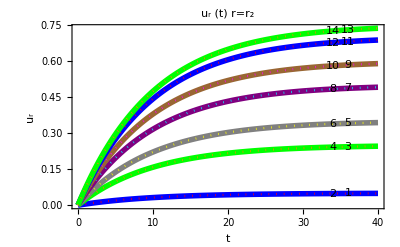
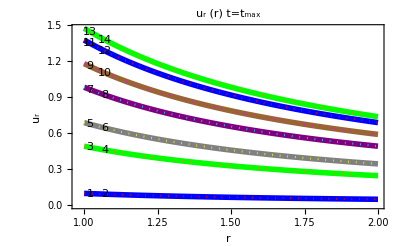

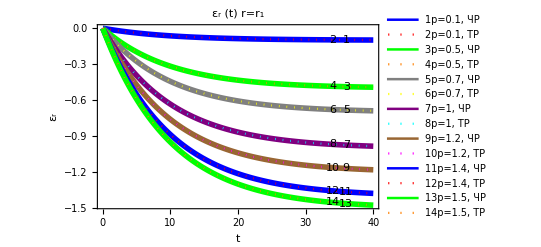
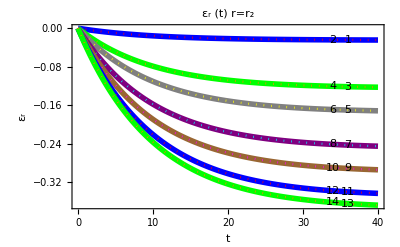

```mathematica
Do[Quiet[figcompare[var,Range[1,Np],Range[1,2*Np],xarr[var]]],{var, MyKeys}]
```

## Power function Case fi[x]=Sqrt[x]

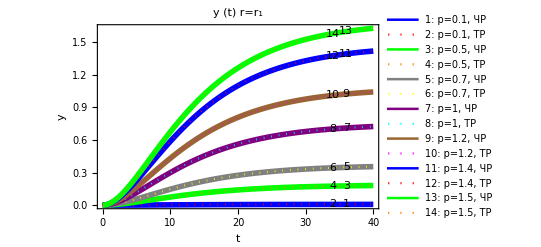
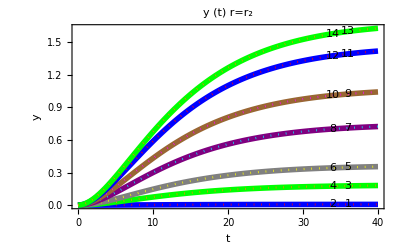
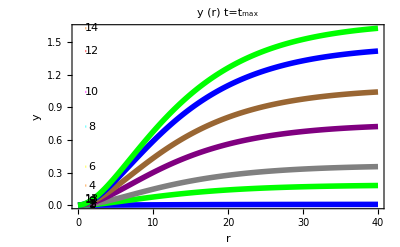

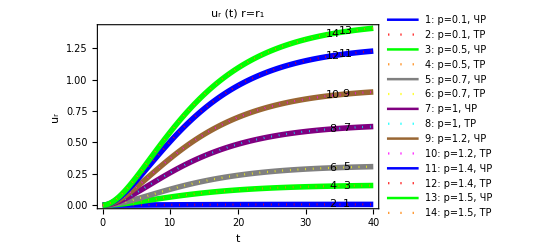
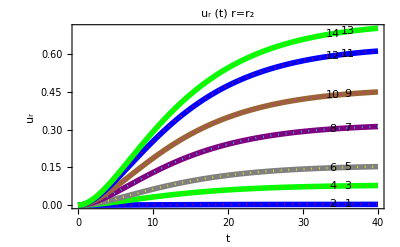
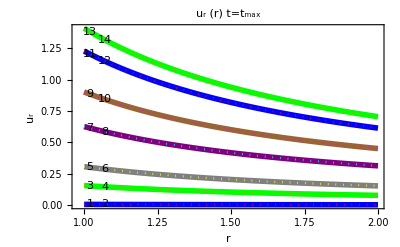

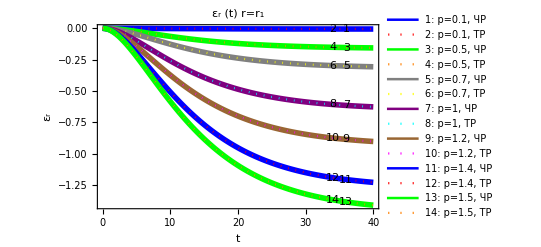
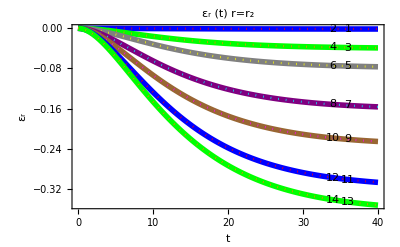

```mathematica
Do[Quiet[figcompare2[var,Range[1,Np],Range[1,2*Np],xarr[var]]],{var, MyKeys}]
```

## Exponential Case fi[x]=σzv(1-Exp[x])

100

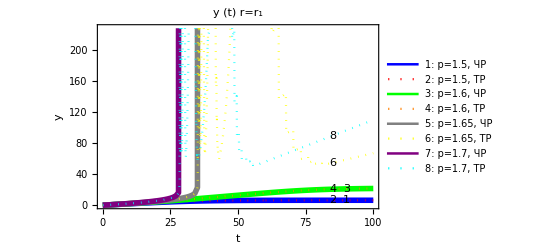
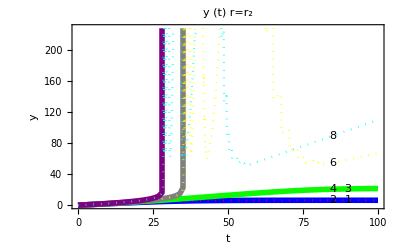
-Graphics--Graphics--Graphics-

```mathematica
tmax=100
figcompare3[Kmyy,Range[1,Np],Range[1,2*Np],xarr[Kmyy]]
```

## Results= Material Function : linear vs nonlinear Log

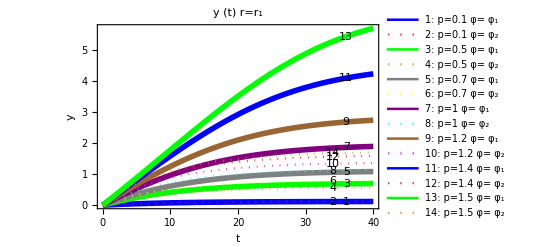
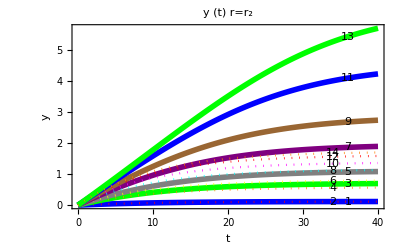
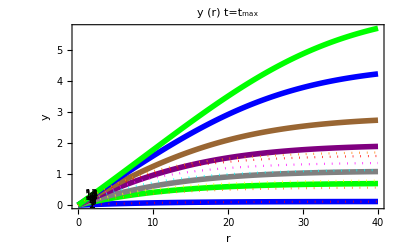

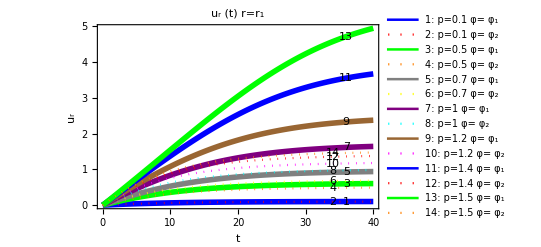
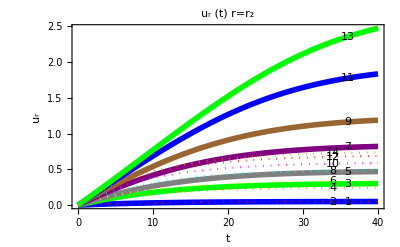
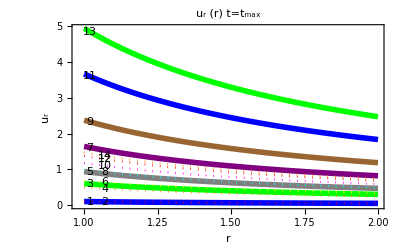

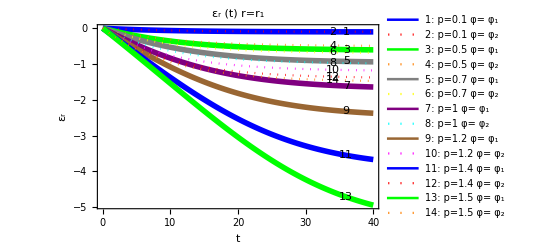
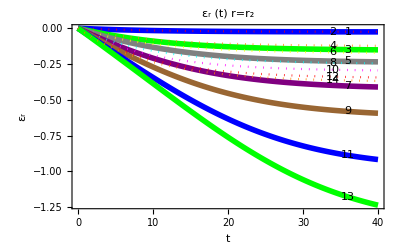

```mathematica
Do[Quiet[figgen[var,Range[1,Np],{1,2},Range[1,2*Np],xarr[var]]],{var, MyKeys}]
```

## Importing/Exporting

```mathematica
Export["table.txt",arr];
myArr=Import["table.txt","Table"]
```

## Experiments on C^0 pressure function

### * D[C^0 function] = Discontinuous function * D[Heaviside function] = Delta function * Π[f] = ∫_0^t Π[t-τ]f'[τ]ⅆτ+f[0]Π[t] *Δp[t]=p_0*Min[t/t_a,1] => ΠΔp=p_0/t_a∫_0^Min[t,t_a] Π[t-τ]ⅆτ => Pdot=√3 d/dt(ΠΔp)=(√3 p_0)/t_a(∫_0^Min[t,t_a] Π'[t-τ]ⅆτ+Π[0]ν(t_a-t))

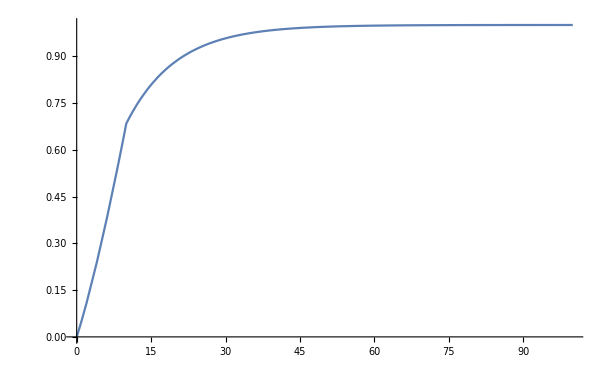

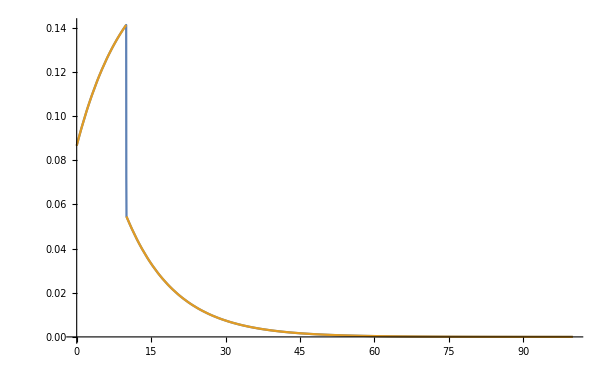

```mathematica
p1[t_,ω_,p0_]:=p0*Min[t/TimeIncr,1];
ΠP[dp_Symbol,dpdt_Symbol,t_?NumberQ,ω_,p_]:=NIntegrate[Π[t-t1]*dpdt[t1,ω,p],{t1,0,t},Method->{Automatic,"SymbolicProcessing"->False}] + Π[t]*dp[0,ω,p]
ΠPC0[dp_Symbol,dpdt_Symbol,t_?NumericQ,tdisc_?NumericQ,ω_, p_]:=Module[{t0=Min[t,tdisc], t1=If[t<tdisc,0,tdisc]},NIntegrate[Π[t-τ]*dpdt[τ,ω,p],{τ,0,t0},Method->{Automatic,"SymbolicProcessing"->False}] ]
PdotMy[t_,tdisc_,p_]:=(Sqrt[3]*p/tdisc)*(NIntegrate[Π'[t-τ],{τ,0,Min[t,tdisc]},Method->{Automatic,"SymbolicProcessing"->False}] + Π[0]*HeavisideTheta[tdisc-t])
Plot[{(*ΠP[dp,dpdt,t,1,1],*)ΠPC0[dp,dpdt,t,TimeIncr, 1,1]},{t,0,tmax}, PlotRange->All]
Plot[{Sqrt[3](ΠPC0[dp,dpdt,t + 0.0001,TimeIncr, 1,1]-ΠPC0[dp,dpdt,t - 0.0001,TimeIncr, 1,1])/0.0002,PdotMy[t,TimeIncr,1]},{t,0,tmax}, PlotRange->All]
```

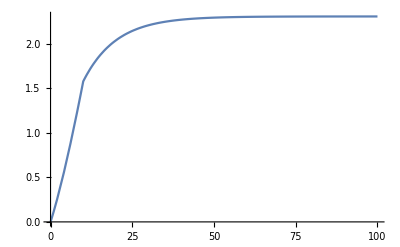

```mathematica
IntegPdot[t_]:=NIntegrate[Pdott[dp,dpdt,τ1,TimeIncr,1],{τ1,0,t},Method->{Automatic,"SymbolicProcessing"->False}]
Plot[{(Sqrt[3]/(1-q))*ΠPC0[dp,dpdt,t,TimeIncr,1, 1]},{t,0,tmax}, PlotRange->All]
```

```mathematica
IntegPdot[1]
PdotMy[1,TimeIncr,1]
```

0.0907919

0.0948439

```mathematica
ToString[φx[[1]]]
```

φ1

```mathematica
Print[Subscript["s",1]"s"]
```

s s_1

```mathematica
arr[[1,1]][Kur]
```

{{{0.,8.66025×10^-11},{1.,0.150608},{2.,0.302377},{3.,0.455231},{4.,0.609056},{5.,0.76371},{6.,0.91905},{7.,1.07493},{8.,1.2312},{9.,1.38764},{10.,1.544},{11.,1.70005},{12.,1.85555},{13.,2.01025},{14.,2.16384},{15.,2.31601},{16.,2.46646},{17.,2.61489},{18.,2.76097},{19.,2.90438},{20.,3.04483},{21.,3.18202},{22.,3.31563},{23.,3.44539},{24.,3.57106},{25.,3.69247},{26.,3.80942},{27.,3.92171},{28.,4.02916},{29.,4.13173},{30.,4.22938},{31.,4.3221},{32.,4.40988},{33.,4.49269},{34.,4.57064},{35.,4.64385},{36.,4.71244},{37.,4.77656},{38.,4.83632},{39.,4.89192},{40.,4.94353},{41.,4.99136},{42.,5.03561},{43.,5.07646},{44.,5.11413},{45.,5.14881},{46.,5.18068},{47.,5.20993},{48.,5.23673},{49.,5.26128},{50.,5.28374},{51.,5.3043},{52.,5.32307},{53.,5.34019},{54.,5.35578},{55.,5.36997},{56.,5.38289},{57.,5.39466},{58.,5.40539},{59.,5.41513},{60.,5.42399},{61.,5.43202},{62.,5.43931},{63.,5.44593},{64.,5.45197},{65.,5.45745},{66.,5.46242},{67.,5.46692},{68.,5.47099},{69.,5.47466},{70.,5.47798},{71.,5.48099},{72.,5.48371},{73.,5.4862},{74.,5.48846},{75.,5.49051},{76.,5.49236},{77.,5.49403},{78.,5.49554},{79.,5.49689},{80.,5.49812},{81.,5.49923},{82.,5.50024},{83.,5.50116},{84.,5.50199},{85.,5.50274},{86.,5.50342},{87.,5.50403},{88.,5.50459},{89.,5.50509},{90.,5.50554},{91.,5.50595},{92.,5.50633},{93.,5.50667},{94.,5.50698},{95.,5.50727},{96.,5.50753},{97.,5.50777},{98.,5.50798},{99.,5.50818},{100.,5.50835}},{{0.,5.7735×10^-11},{1.,0.100405},{2.,0.201585},{3.,0.303487},{4.,0.406037},{5.,0.50914},{6.,0.6127},{7.,0.716623},{8.,0.820802},{9.,0.925091},{10.,1.02933},{11.,1.13336},{12.,1.23703},{13.,1.34017},{14.,1.44256},{15.,1.54401},{16.,1.64431},{17.,1.74326},{18.,1.84064},{19.,1.93625},{20.,2.02989},{21.,2.12135},{22.,2.21042},{23.,2.29692},{24.,2.38071},{25.,2.46165},{26.,2.53961},{27.,2.61447},{28.,2.68611},{29.,2.75449},{30.,2.81959},{31.,2.8814},{32.,2.93992},{33.,2.99513},{34.,3.04709},{35.,3.0959},{36.,3.14163},{37.,3.18437},{38.,3.22422},{39.,3.26128},{40.,3.29569},{41.,3.32758},{42.,3.35707},{43.,3.38431},{44.,3.40942},{45.,3.43254},{46.,3.45378},{47.,3.47328},{48.,3.49115},{49.,3.50752},{50.,3.5225},{51.,3.5362},{52.,3.54871},{53.,3.56012},{54.,3.57052},{55.,3.57998},{56.,3.58859},{57.,3.59644},{58.,3.60359},{59.,3.61009},{60.,3.61599},{61.,3.62134},{62.,3.6262},{63.,3.63062},{64.,3.63464},{65.,3.6383},{66.,3.64161},{67.,3.64462},{68.,3.64733},{69.,3.64978},{70.,3.65199},{71.,3.65399},{72.,3.65581},{73.,3.65747},{74.,3.65897},{75.,3.66034},{76.,3.66157},{77.,3.66269},{78.,3.66369},{79.,3.6646},{80.,3.66541},{81.,3.66615},{82.,3.66682},{83.,3.66744},{84.,3.66799},{85.,3.66849},{86.,3.66895},{87.,3.66936},{88.,3.66973},{89.,3.67006},{90.,3.67036},{91.,3.67063},{92.,3.67088},{93.,3.67111},{94.,3.67132},{95.,3.67151},{96.,3.67169},{97.,3.67184},{98.,3.67199},{99.,3.67212},{100.,3.67223}},{{0.,4.33013×10^-11},{1.,0.0753039},{2.,0.151189},{3.,0.227615},{4.,0.304528},{5.,0.381855},{6.,0.459525},{7.,0.537467},{8.,0.615602},{9.,0.693818},{10.,0.771998},{11.,0.850023},{12.,0.927775},{13.,1.00512},{14.,1.08192},{15.,1.158},{16.,1.23323},{17.,1.30745},{18.,1.38048},{19.,1.45219},{20.,1.52242},{21.,1.59101},{22.,1.65782},{23.,1.72269},{24.,1.78553},{25.,1.84624},{26.,1.90471},{27.,1.96085},{28.,2.01458},{29.,2.06586},{30.,2.11469},{31.,2.16105},{32.,2.20494},{33.,2.24635},{34.,2.28532},{35.,2.32192},{36.,2.35622},{37.,2.38828},{38.,2.41816},{39.,2.44596},{40.,2.47177},{41.,2.49568},{42.,2.5178},{43.,2.53823},{44.,2.55706},{45.,2.5744},{46.,2.59034},{47.,2.60496},{48.,2.61837},{49.,2.63064},{50.,2.64187},{51.,2.65215},{52.,2.66153},{53.,2.67009},{54.,2.67789},{55.,2.68498},{56.,2.69144},{57.,2.69733},{58.,2.70269},{59.,2.70757},{60.,2.71199},{61.,2.71601},{62.,2.71965},{63.,2.72297},{64.,2.72598},{65.,2.72872},{66.,2.73121},{67.,2.73346},{68.,2.7355},{69.,2.73733},{70.,2.73899},{71.,2.74049},{72.,2.74186},{73.,2.7431},{74.,2.74423},{75.,2.74525},{76.,2.74618},{77.,2.74701},{78.,2.74777},{79.,2.74845},{80.,2.74906},{81.,2.74961},{82.,2.75012},{83.,2.75058},{84.,2.75099},{85.,2.75137},{86.,2.75171},{87.,2.75202},{88.,2.75229},{89.,2.75254},{90.,2.75277},{91.,2.75298},{92.,2.75316},{93.,2.75333},{94.,2.75349},{95.,2.75363},{96.,2.75376},{97.,2.75388},{98.,2.75399},{99.,2.75409},{100.,2.75417}},{{1.,5.50835},{1.01,5.45381},{1.02,5.40034},{1.03,5.34791},{1.04,5.29649},{1.05,5.24605},{1.06,5.19655},{1.07,5.14799},{1.08,5.10032},{1.09,5.05353},{1.1,5.00759},{1.11,4.96248},{1.12,4.91817},{1.13,4.87464},{1.14,4.83188},{1.15,4.78987},{1.16,4.74858},{1.17,4.70799},{1.18,4.66809},{1.19,4.62886},{1.2,4.59029},{1.21,4.55235},{1.22,4.51504},{1.23,4.47833},{1.24,4.44222},{1.25,4.40668},{1.26,4.3717},{1.27,4.33728},{1.28,4.3034},{1.29,4.27004},{1.3,4.23719},{1.31,4.20485},{1.32,4.17299},{1.33,4.14162},{1.34,4.11071},{1.35,4.08026},{1.36,4.05026},{1.37,4.02069},{1.38,3.99156},{1.39,3.96284},{1.4,3.93453},{1.41,3.90663},{1.42,3.87912},{1.43,3.85199},{1.44,3.82524},{1.45,3.79886},{1.46,3.77284},{1.47,3.74718},{1.48,3.72186},{1.49,3.69688},{1.5,3.67223},{1.51,3.64791},{1.52,3.62391},{1.53,3.60023},{1.54,3.57685},{1.55,3.55377},{1.56,3.53099},{1.57,3.5085},{1.58,3.4863},{1.59,3.46437},{1.6,3.44272},{1.61,3.42133},{1.62,3.40021},{1.63,3.37935},{1.64,3.35875},{1.65,3.33839},{1.66,3.31828},{1.67,3.29841},{1.68,3.27878},{1.69,3.25938},{1.7,3.2402},{1.71,3.22126},{1.72,3.20253},{1.73,3.18402},{1.74,3.16572},{1.75,3.14763},{1.76,3.12974},{1.77,3.11206},{1.78,3.09458},{1.79,3.07729},{1.8,3.06019},{1.81,3.04329},{1.82,3.02656},{1.83,3.01003},{1.84,2.99367},{1.85,2.97749},{1.86,2.96148},{1.87,2.94564},{1.88,2.92997},{1.89,2.91447},{1.9,2.89913},{1.91,2.88395},{1.92,2.86893},{1.93,2.85407},{1.94,2.83935},{1.95,2.82479},{1.96,2.81038},{1.97,2.79612},{1.98,2.78199},{1.99,2.76801},{2.,2.75417}}}